# Challenges W11 - Cameron Embree (4/9/14)

Challenge 1: A sequence of random numbers distributed uniformly on [0,1) should have mean 1/2 and standard deviation 1/12.  Check the mean and standard devation for 100,000 numbers using the Minimal Standard Random Generator and IBMs randu

```mathematica
(*Challenge 1 solution by:*)
```

```mathematica
Clear["Global`*"]
Print["Minimal Standard Random Generator results: "]
triples={{1702,952,10001},{2^16+3,0,2^31},{7^5,0,2^31}};
{a,b,m}=triples[[2]];
seed=30;
randomnumbers=RecurrenceTable[{x[n]==Mod[a*x[n-1]+b,m],x[0]==seed} ,x,{n,0,100000}]/m //N;
mean=Mean[randomnumbers];
sd=StandardDeviation[randomnumbers];

Print["Mean is: ",mean," and should be: ",0.5]
Print["Standard Deviation is: ",sd, " and should be: ", 1/12//N]


Print["IBM randu results: "]
{a,b,m}=triples[[3]];
seed=30;
randomnumbers=RecurrenceTable[{x[n]==Mod[a*x[n-1]+b,m],x[0]==seed} ,x,{n,0,100000}]/m //N;
mean=Mean[randomnumbers];
sd=StandardDeviation[randomnumbers];

Print["Mean is: ",mean," and should be: ",0.5]
Print["Standard Deviation is: ",sd, " and should be: ", 1/12//N]
```

Minimal Standard Random Generator results:

Mean is: 0.49949 and should be: 0.5

Standard Deviation is: 0.288588 and should be: 0.0833333

IBM randu results:

Mean is: 0.500654 and should be: 0.5

Standard Deviation is: 0.288358 and should be: 0.0833333

Challenge 2:  Use random sampling  to determine  the probability thet the quadratic equation ax^2+bx+c=0 will have real roots if a,b,c and are uniformly drawn from the interval [-1,1]

```mathematica
(*Challenge 2 solution by:*)
```

```mathematica
count[y_]:=CountRoots[RandomReal[{-1,1}]*x^2+RandomReal[{-1,1}]*x+RandomReal[{-1,1}],x]

res=Array[count,20000];
Count[res,2]/Length[res]//N
```

0.62385

Challenge 3: The birthday pardox:  Use random trials  to determine the smallest number of persons required for the probability that at least 2 share the same birthday be  greater than .5.

```mathematica
(*Challenge 3 solution by:*)
```

```mathematica
genBDays[i_]:=RandomInteger[{365},i]
numOfBDays=genBDays[100000]
```

{204,56,165,132,108,359,95,298,363,342,290,93,328,191,89,120,161,278,102,68,195,229,209,38,187,253,119,244,211,51,223,341,221,173,62,138,123,7,305,351,«99920»,23,227,198,243,216,260,307,256,348,0,91,174,231,54,147,343,347,92,124,280,100,45,14,130,64,63,5,265,272,196,167,228,111,130,275,52,87,55,185,163}

Challenge 4:  Find the area bounded by two parabolas x^2-x+.5 and -x^2+x+.5

Expected answer: 126.555

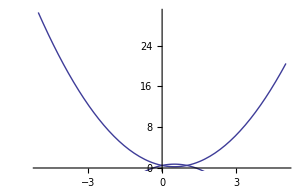

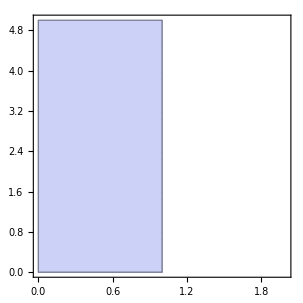

Data size: 10

{{0.451568,0.120724},{0.369304,0.324489},{0.719722,0.595183},{0.352662,0.900724},{0.462691,0.727885},{0.945449,0.793336},{0.907212,0.0270624},{0.402255,0.102775},{0.831634,0.364054},{0.321929,0.0327706}}

0

```mathematica
(*Challenge 4 solution by:*)
f[x_]:=x^2-x+0.5
g[x_]:=-x^2+x+0.5
Print["Expected answer: ",NIntegrate[Abs[f[x]-g[x]],{x,0,2 Pi}]]

Show[
Plot[x^2-x+0.5,{x,-5,5}],
Plot[-x^2+x+0.5,{x,-5,5}]
]
RegionPlot[-y-x^2+x+0.5>=-y+x^2-x+0.5,{x,0,2},{y,0,5}]

n=10 ;(*Sample size*)
Print["Data size: ",n]
samples=RandomReal[{0,1},{n,2}]

Count[samples,_?(-#[[2]]-#[[1]]^2+#[[1]]+0.5<-#[[2]]+#[[1]]^2-#[[1]]+0.5)&]
```

Challenge 5:  Use Monte Carlo integration to approximate the area of a four dimensional sphere of radius 1

```mathematica
(*Challenge 5 solution by:*)
```

```mathematica
n=100000;
samples=RandomReal[{-1,1},{n,4}];

(* 4-D Sphere w/ radius 1 : x^2+y^2+z^2+j^2 ≤ 1 *)
Count[samples,_?(Sqrt[#[[1]]^2+#[[2]]^2+#[[3]]^2+#[[4]]^2]<=1&)]/n //N
```

0.30875

Challenge 6: What’s the probability that a 2x2 matrix  with entries from the interval [0,1] will have ra postive determinant?

```mathematica
(*Challenge 6 solution by:*)
```

Challenge 7: Design a Monte Carlo simulation to the estimate the probability of a rondom walk reaching the top of a given interval [-b,a].  Carry out 10000 random walks.  Do for the intervals [-2,5],[-5,3],[-8,3]

```mathematica
(*Challenge 7 solution by:*)
```

Challenge 9:  The arcsine law of brownian motion holds that for 0<t1<t2, the probability that a path does not cross zero in the time interval [t1,t2] is 2/pi arcsine sqrt[t1/t2].  Carry out a monte carlo simulation ef this probability by using 10000 paths with each time step being .01.  Compare the result of your simulation with the arcsine law for brownian motion for the intevals 3<t<5, 2<t<10, 8<t<10.

```mathematica
(*Challenge 8 solution by:*)
```